```mathematica
Clear[KSx0,KSx1,KSx2,KSx3]
```

{CYLx0→x0,CYLx1→ⅇ^x1+R0,CYLx2→x2,CYLx3→x3}

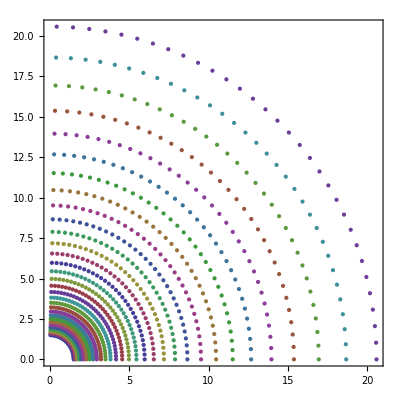

```mathematica
(* coordinate conversion *)
cx0=CYLx0==x0;
cx3=CYLx3==x3;
cx1=CYLx1==R0+Exp[x1];
cx2=CYLx2==x2;
suborg={cx0[[1]]->cx0[[2]],cx1[[1]]->cx1[[2]],cx2[[1]]->cx2[[2]],cx3[[1]]->cx3[[2]]}
grid=Table[{cx2[[2]],cx1[[2]]}/.{R0->.5},{x1,0,3,.1},{x2,0,π/2,.05}];
ListPolarPlot[grid,Frame->True]
```

```mathematica
(* inverse transformation *)
subinv={
icx0=Solve[cx0,x0][[1,1]],
icx1=x1->Log[KSx1-R0](* Solve[cx1,x1] *),
icx2=Solve[cx2,x2][[1,1]],
icx3=Solve[cx3,x3][[1,1]]}
```

{x0→CYLx0,x1→Log[KSx1-R0],x2→CYLx2,x3→CYLx3}

```mathematica
XKSMKS={{D[cx0[[2]],x0],D[cx0[[2]],x1],D[cx0[[2]],x2],D[cx0[[2]],x3]},
{D[cx1[[2]],x0],D[cx1[[2]],x1],D[cx1[[2]],x2],D[cx1[[2]],x3]},
{D[cx2[[2]],x0],D[cx2[[2]],x1],D[cx2[[2]],x2],D[cx2[[2]],x3]},
{D[cx3[[2]],x0],D[cx3[[2]],x1],D[cx3[[2]],x2],D[cx3[[2]],x3]}}/.subinv;
TableForm[XKSMKS]
```

1 | 0 | 0 | 0
0 | KSx1-R0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
(* no coupling between various coordinates so this is simple *)
XMKSKS=Inverse[XKSMKS];
TableForm[XMKSKS]
```

1 | 0 | 0 | 0
0 | 1/(KSx1-R0) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
(* done with dXdX arrays so far *)
```

```mathematica
(* cylindrical g_munu (-+++) *)
scoor = {r->x1,z->x2, ϕ->x3};
g00=-1;
g11=1;
g22=1;
g33=r^2;
g01=g02=g03=g10=g12=g13=g20=g21=g23=g30=g31=g32=0;
```

```mathematica
(* matrix form *)
gKS=Simplify[{{g00,g01,g02,g03},{g10,g11,g12,g13},{g20,g21,g22,g23},{g30,g31,g32,g33}}];
gKS=gKS/.scoor;
MatrixForm[gKS]
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | x1^2)

```mathematica
(* inversed metric g^munu *)
MatrixForm[GKS=Simplify[Inverse[gKS]]]
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1/x1^2)

```mathematica
GMKS=GKS;
For[i=1,i<=4,i++,
For[j=1,j<=4,j++,
GMKS[[i,j]]=0;
For[k=1,k<=4,k++,
For[l=1,l<=4,l++,
GMKS[[i,j]]=GMKS[[i,j]]+ XMKSKS[[i,k]] XMKSKS[[j,l]] GKS[[k,l]];
]
]
]
]
(* substituting MKS coordinates *)
GMKS=GMKS/.suborg;
TableForm[Simplify[GMKS]]
```

-1 | 0 | 0 | 0
0 | 1/(KSx1-R0)^2 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1/x1^2

```mathematica
TableForm[gMKS=Simplify[Inverse[GMKS]]]
```

-1 | 0 | 0 | 0
0 | (KSx1-R0)^2 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | x1^2

```mathematica
(* coming back to original notation *)
g=gMKS;
G=GMKS;
```

```mathematica
(* matrix determinant *)
gdet=Simplify[Sqrt[-Det[g]]]
```

√((KSx1-R0)^2 x1^2)

```mathematica
(*matrix determinant log derivatives*)
dlgdet=Simplify[{D[gdet,x1]/gdet,D[gdet,x2]/gdet,D[gdet,x3]/gdet}]
```

{1/x1,0,0}

```mathematica
(* auxiliary matrices of derivatives *)
dgdx = {D[g,x0],D[g,x1],D[g,x2],D[g,x3]};
```

```mathematica
(* Christofells with 3 lower indices *)
γ=Table[(dgdx[[k,i,j]]+dgdx[[j,i,k]]-dgdx[[i,j,k]])/2,{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
(* Christofells with 1st index up *)
Γ=Simplify[Table[Sum[G[[i,b]]γ[[b,j,k]],{b,1,4}],{i,1,4},{j,1,4},{k,1,4}]];
```

```mathematica
(*************** CForms ******************)
```

```mathematica
(* coordinate transformations MCYL1 -> CYL *)
TableForm[{
CForm[suborg[[1,1]]],"="CForm[suborg[[1,2]]],";",
CForm[suborg[[2,1]]],"="CForm[suborg[[2,2]]],";",
CForm[suborg[[3,1]]],"="CForm[suborg[[3,2]]],";",
CForm[suborg[[4,1]]],"="CForm[suborg[[4,2]]],";"}]
```

CYLx0
= x0
;
CYLx1
= Power(E,x1) + R0
;
CYLx2
= x2
;
CYLx3
= x3
;

```mathematica
(* coordinate transformations CYL -> MCYL1 *)
TableForm[{
CForm[subinv[[1,1]]],"="CForm[subinv[[1,2]]],";",
CForm[subinv[[2,1]]],"="CForm[subinv[[2,2]]],";",
CForm[subinv[[3,1]]],"="CForm[subinv[[3,2]]],";",
CForm[subinv[[4,1]]],"="CForm[subinv[[4,2]]],";"}]
```

x0
= CYLx0
;
x1
= Log(KSx1 - R0)
;
x2
= CYLx2
;
x3
= CYLx3
;

```mathematica
substC={
"E"->"exp(1.0)"
};
```

```mathematica
(* determinant in CForm *)
StringReplace[ToString[CForm[gdet]],substC]
```

Sqrt(Power(KSx1 - R0,2)*Power(x1,2))

```mathematica
(* dlog determinant in CForm *)
TableForm[{
";if(idim==0) return " CForm[dlgdet[[1]]],
";if(idim==1) return " CForm[dlgdet[[2]]],
";if(idim==2) return " CForm[dlgdet[[3]]],";"}]
```

;if(idim==0) return  1/x1
;if(idim==1) return  0
;if(idim==2) return  0
;

```mathematica
(* metric in CForm *)
gC=TableForm[{
";g[0][0]="CForm[g[[1,1]]],
";g[0][1]="CForm[g[[1,2]]],
";g[0][2]="CForm[g[[1,3]]],
";g[0][3]="CForm[g[[1,4]]],
";g[1][0]="CForm[g[[2,1]]],
";g[1][1]="CForm[g[[2,2]]],
";g[1][2]="CForm[g[[2,3]]],
";g[1][3]="CForm[g[[2,4]]],
";g[2][0]="CForm[g[[3,1]]],
";g[2][1]="CForm[g[[3,2]]],
";g[2][2]="CForm[g[[3,3]]],
";g[2][3]="CForm[g[[3,4]]],
";g[3][0]="CForm[g[[4,1]]],
";g[3][1]="CForm[g[[4,2]]],
";g[3][2]="CForm[g[[4,3]]],
";g[3][3]="CForm[g[[4,4]]],";"
}]
```

;g[0][0]= -1
;g[0][1]= 0
;g[0][2]= 0
;g[0][3]= 0
;g[1][0]= 0
;g[1][1]= Power(KSx1 - R0,2)
;g[1][2]= 0
;g[1][3]= 0
;g[2][0]= 0
;g[2][1]= 0
;g[2][2]= 1
;g[2][3]= 0
;g[3][0]= 0
;g[3][1]= 0
;g[3][2]= 0
;g[3][3]= Power(x1,2)
;

```mathematica
(* inversed metric in CForm *)
GC=TableForm[{
";G[0][0]="CForm[G[[1,1]]],
";G[0][1]="CForm[G[[1,2]]],
";G[0][2]="CForm[G[[1,3]]],
";G[0][3]="CForm[G[[1,4]]],
";G[1][0]="CForm[G[[2,1]]],
";G[1][1]="CForm[G[[2,2]]],
";G[1][2]="CForm[G[[2,3]]],
";G[1][3]="CForm[G[[2,4]]],
";G[2][0]="CForm[G[[3,1]]],
";G[2][1]="CForm[G[[3,2]]],
";G[2][2]="CForm[G[[3,3]]],
";G[2][3]="CForm[G[[3,4]]],
";G[3][0]="CForm[G[[4,1]]],
";G[3][1]="CForm[G[[4,2]]],
";G[3][2]="CForm[G[[4,3]]],
";G[3][3]="CForm[G[[4,4]]],";"
}]
```

;G[0][0]= -1
;G[0][1]= 0
;G[0][2]= 0
;G[0][3]= 0
;G[1][0]= 0
;G[1][1]= Power(KSx1 - R0,-2)
;G[1][2]= 0
;G[1][3]= 0
;G[2][0]= 0
;G[2][1]= 0
;G[2][2]= 1
;G[2][3]= 0
;G[3][0]= 0
;G[3][1]= 0
;G[3][2]= 0
;G[3][3]= Power(x1,-2)
;

```mathematica
(* Christoffels in CForm *)
ΓC=TableForm[{
";Krzys[0][0][0]="CForm[Γ[[1,1,1]]],
";Krzys[0][0][1]="CForm[Γ[[1,1,2]]],
";Krzys[0][0][2]="CForm[Γ[[1,1,3]]],
";Krzys[0][0][3]="CForm[Γ[[1,1,4]]],
";Krzys[0][1][0]="CForm[Γ[[1,2,1]]],
";Krzys[0][1][1]="CForm[Γ[[1,2,2]]],
";Krzys[0][1][2]="CForm[Γ[[1,2,3]]],
";Krzys[0][1][3]="CForm[Γ[[1,2,4]]],
";Krzys[0][2][0]="CForm[Γ[[1,3,1]]],
";Krzys[0][2][1]="CForm[Γ[[1,3,2]]],
";Krzys[0][2][2]="CForm[Γ[[1,3,3]]],
";Krzys[0][2][3]="CForm[Γ[[1,3,4]]],
";Krzys[0][3][0]="CForm[Γ[[1,4,1]]],
";Krzys[0][3][1]="CForm[Γ[[1,4,2]]],
";Krzys[0][3][2]="CForm[Γ[[1,4,3]]],
";Krzys[0][3][3]="CForm[Γ[[1,4,4]]],

";Krzys[1][0][0]="CForm[Γ[[2,1,1]]],
";Krzys[1][0][1]="CForm[Γ[[2,1,2]]],
";Krzys[1][0][2]="CForm[Γ[[2,1,3]]],
";Krzys[1][0][3]="CForm[Γ[[2,1,4]]],
";Krzys[1][1][0]="CForm[Γ[[2,2,1]]],
";Krzys[1][1][1]="CForm[Γ[[2,2,2]]],
";Krzys[1][1][2]="CForm[Γ[[2,2,3]]],
";Krzys[1][1][3]="CForm[Γ[[2,2,4]]],
";Krzys[1][2][0]="CForm[Γ[[2,3,1]]],
";Krzys[1][2][1]="CForm[Γ[[2,3,2]]],
";Krzys[1][2][2]="CForm[Γ[[2,3,3]]],
";Krzys[1][2][3]="CForm[Γ[[2,3,4]]],
";Krzys[1][3][0]="CForm[Γ[[2,4,1]]],
";Krzys[1][3][1]="CForm[Γ[[2,4,2]]],
";Krzys[1][3][2]="CForm[Γ[[2,4,3]]],
";Krzys[1][3][3]="CForm[Γ[[2,4,4]]],

";Krzys[2][0][0]="CForm[Γ[[3,1,1]]],
";Krzys[2][0][1]="CForm[Γ[[3,1,2]]],
";Krzys[2][0][2]="CForm[Γ[[3,1,3]]],
";Krzys[2][0][3]="CForm[Γ[[3,1,4]]],
";Krzys[2][1][0]="CForm[Γ[[3,2,1]]],
";Krzys[2][1][1]="CForm[Γ[[3,2,2]]],
";Krzys[2][1][2]="CForm[Γ[[3,2,3]]],
";Krzys[2][1][3]="CForm[Γ[[3,2,4]]],
";Krzys[2][2][0]="CForm[Γ[[3,3,1]]],
";Krzys[2][2][1]="CForm[Γ[[3,3,2]]],
";Krzys[2][2][2]="CForm[Γ[[3,3,3]]],
";Krzys[2][2][3]="CForm[Γ[[3,3,4]]],
";Krzys[2][3][0]="CForm[Γ[[3,4,1]]],
";Krzys[2][3][1]="CForm[Γ[[3,4,2]]],
";Krzys[2][3][2]="CForm[Γ[[3,4,3]]],
";Krzys[2][3][3]="CForm[Γ[[3,4,4]]],

";Krzys[3][0][0]="CForm[Γ[[4,1,1]]],
";Krzys[3][0][1]="CForm[Γ[[4,1,2]]],
";Krzys[3][0][2]="CForm[Γ[[4,1,3]]],
";Krzys[3][0][3]="CForm[Γ[[4,1,4]]],
";Krzys[3][1][0]="CForm[Γ[[4,2,1]]],
";Krzys[3][1][1]="CForm[Γ[[4,2,2]]],
";Krzys[3][1][2]="CForm[Γ[[4,2,3]]],
";Krzys[3][1][3]="CForm[Γ[[4,2,4]]],
";Krzys[3][2][0]="CForm[Γ[[4,3,1]]],
";Krzys[3][2][1]="CForm[Γ[[4,3,2]]],
";Krzys[3][2][2]="CForm[Γ[[4,3,3]]],
";Krzys[3][2][3]="CForm[Γ[[4,3,4]]],
";Krzys[3][3][0]="CForm[Γ[[4,4,1]]],
";Krzys[3][3][1]="CForm[Γ[[4,4,2]]],
";Krzys[3][3][2]="CForm[Γ[[4,4,3]]],
";Krzys[3][3][3]="CForm[Γ[[4,4,4]]],
";"
}]
```

;Krzys[0][0][0]= 0
;Krzys[0][0][1]= 0
;Krzys[0][0][2]= 0
;Krzys[0][0][3]= 0
;Krzys[0][1][0]= 0
;Krzys[0][1][1]= 0
;Krzys[0][1][2]= 0
;Krzys[0][1][3]= 0
;Krzys[0][2][0]= 0
;Krzys[0][2][1]= 0
;Krzys[0][2][2]= 0
;Krzys[0][2][3]= 0
;Krzys[0][3][0]= 0
;Krzys[0][3][1]= 0
;Krzys[0][3][2]= 0
;Krzys[0][3][3]= 0
;Krzys[1][0][0]= 0
;Krzys[1][0][1]= 0
;Krzys[1][0][2]= 0
;Krzys[1][0][3]= 0
;Krzys[1][1][0]= 0
;Krzys[1][1][1]= 0
;Krzys[1][1][2]= 0
;Krzys[1][1][3]= 0
;Krzys[1][2][0]= 0
;Krzys[1][2][1]= 0
;Krzys[1][2][2]= 0
;Krzys[1][2][3]= 0
;Krzys[1][3][0]= 0
;Krzys[1][3][1]= 0
;Krzys[1][3][2]= 0
;Krzys[1][3][3]= -(x1/Power(KSx1 - R0,2))
;Krzys[2][0][0]= 0
;Krzys[2][0][1]= 0
;Krzys[2][0][2]= 0
;Krzys[2][0][3]= 0
;Krzys[2][1][0]= 0
;Krzys[2][1][1]= 0
;Krzys[2][1][2]= 0
;Krzys[2][1][3]= 0
;Krzys[2][2][0]= 0
;Krzys[2][2][1]= 0
;Krzys[2][2][2]= 0
;Krzys[2][2][3]= 0
;Krzys[2][3][0]= 0
;Krzys[2][3][1]= 0
;Krzys[2][3][2]= 0
;Krzys[2][3][3]= 0
;Krzys[3][0][0]= 0
;Krzys[3][0][1]= 0
;Krzys[3][0][2]= 0
;Krzys[3][0][3]= 0
;Krzys[3][1][0]= 0
;Krzys[3][1][1]= 0
;Krzys[3][1][2]= 0
;Krzys[3][1][3]= 1/x1
;Krzys[3][2][0]= 0
;Krzys[3][2][1]= 0
;Krzys[3][2][2]= 0
;Krzys[3][2][3]= 0
;Krzys[3][3][0]= 0
;Krzys[3][3][1]= 1/x1
;Krzys[3][3][2]= 0
;Krzys[3][3][3]= 0
;